## TC Hamiltonian

```mathematica
(*Constants*)
bsize=25;ω0=1.0; ωc = 1.0; K = 3;j = 0.07;
(*Identity matrices for TLS and QHO*)
idTSS=SparseArray[IdentityMatrix[2]];
idHO=SparseArray[IdentityMatrix[bsize]];

(*TLS initial Hamiltonian*)
H0TSS=SparseArray[Band[{1,1}]->{ω0/2,-ω0/2}];
(*QHO Hamiltonian*)
H0HO=ωc * SparseArray[Band[{1,1}]->Table[n+1/2,{n,0,bsize-1}]];
(*TLS raising and lowering operators*)
σm={{0,0},{1,0}};
σp={{0,1},{0,0}};

(*Annihilation operator definition*)
a=SparseArray[Band[{1,2}]->Table[Sqrt[n],{n,1,bsize-1}],{bsize,bsize}]; 

(*Scaled harmonic oscillator Hamiltonian, using convention with TLS on the left.*)
Htot = KroneckerProduct[IdentityMatrix[2^K], H0HO];

Do[
(*Tensor product adjustment for the i-th TLS*)
leftIds=If[i>1,Table[idTSS,{i-1}],{IdentityMatrix[1]}];
rightIds=If[i<K,Table[idTSS,{K-i}],{IdentityMatrix[1]}];
(*TLS Hamiltonian for the i-th TLS*)
H0TSSi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,H0TSS],Sequence@@rightIds];
(*Print[Normal[H0TSSi]//MatrixForm];*)
(*Adding ith TLS Hamiltonian to the total Hamiltonian*)
Htot+=KroneckerProduct[H0TSSi,idHO];

σpi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,σp],Sequence@@rightIds];σmi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,σm],Sequence@@rightIds];
Htot+=j*(KroneckerProduct[σpi,a]+KroneckerProduct[σmi,a†]);
,{i,K}];
```

### Initial State

```mathematica
ψ0[w_,x0_]=1/Sqrt[Sqrt[ π]w] Exp[-(x-x0)^2/(2 w^2)];(*Define initial Gaussian state*)
EigState[n_, x_]=π^(-1/4)/Sqrt[2^n n!] Exp[-x^2/2]HermiteH[n,x];
coeff[n_,w_,x0_]:=NIntegrate[EigState[n, x]ψ0[w,x0],{x,-∞,∞},PrecisionGoal->6,AccuracyGoal->5];
(*ψ0HO=Table[coeff[n,1,0],{n,0,bsize-1}];*)
ψ0HO=SparseArray[{1->1.0},bsize];
(*α=3.5;
ψ0HO=Table[Exp[-Abs[α]^2/2]*(α^n/Sqrt[n!]),{n,0,bsize-1}]; *)(*in number/fock basis*)
Print[Total[ψ0HO^2]];

(*excited states in TSS and ___ in the QHO*)
ψ0Vec= (KroneckerProduct[{1, 0},  {1, 0},{1, 0},ψ0HO]) //Flatten
(*
ψ0Vec= 1/√6 * ((KroneckerProduct[{1, 0}, {1, 0}, {0, 1}, {0, 1},ψ0HO]) + 
(KroneckerProduct[{1, 0}, {0, 1}, {1, 0}, {0, 1},ψ0HO]) + 
(KroneckerProduct[{1, 0}, {0, 1},  {0, 1},{1, 0},ψ0HO]) + 
(KroneckerProduct[{0, 1}, {1, 0},  {0, 1},{1, 0},ψ0HO])+ 
(KroneckerProduct[{0, 1}, {1, 0},  {1, 0},{0, 1},ψ0HO] )+
(KroneckerProduct[{0, 1}, {0, 1},  {1, 0},{1, 0},ψ0HO])) // Flatten *)
```

1.

SparseArray[…]

### Observable Matrices

#### Oscillator Position

```mathematica
xM=KroneckerProduct[IdentityMatrix[2^K],1/Sqrt[2](a†+a)];(*Position of the oscillator*)
(*Expected x value for initial state*)
ConjugateTranspose[ψ0Vec].xM.ψ0Vec
```

0.

#### Projection Operator Construction

```mathematica
excitedStateProjection[i_Integer]:=Module[
{
idTSS=IdentityMatrix[2],
partialExcitedProj={{1,0},{0,0}},
leftIds,rightIds,excitedProj
},
leftIds=If[i>1,Table[idTSS,{i-1}],{IdentityMatrix[1]}];
rightIds=If[i<K,Table[idTSS,{K-i}],{IdentityMatrix[1]}];
excitedProj=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,partialExcitedProj,Sequence@@rightIds], idHO];
excitedProj  (*Return the constructed operator*);

excitedProj]
(*excitedStateProjection[1]//MatrixForm*)
```

### Propagation

#### Oscillator Expected Position

```mathematica
stateVector[t_] := MatrixExp[-I * Htot * t, ψ0Vec];
tMax =2000; 
tRange=Range[0,tMax,1.0];
ψs=ParallelTable[stateVector[t],{t,tRange}];
(*xAve=Table[Conjugate[ψs[[n]]].xM.ψs[[n]],{n,Length@tRange}];
ListLinePlot[{tRange,xAve//Re}//Transpose, ImageSize->Full]*)
```

#### Expected Excited State Populations

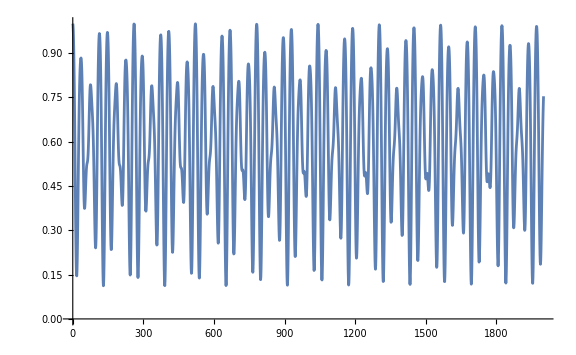

```mathematica
pExcited1 = excitedStateProjection[1];
xAve=Table[Conjugate[ψs[[n]]].pExcited1.ψs[[n]],{n,Length@tRange}];
ListLinePlot[{tRange,xAve//Re}//Transpose, ImageSize->Large]
(*pExcited2 = excitedStateProjection[2];
xAve=Table[Conjugate[ψs[[n]]].pExcited2.ψs[[n]],{n,Length@tRange}];
ListLinePlot[{tRange,xAve//Re}//Transpose]*)
```

### Superradiance

We keep the same initial state, but now we plot the photon emission statistics. We also change our time-scale as needed.

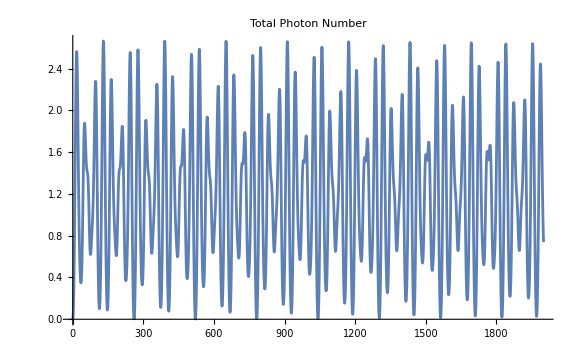

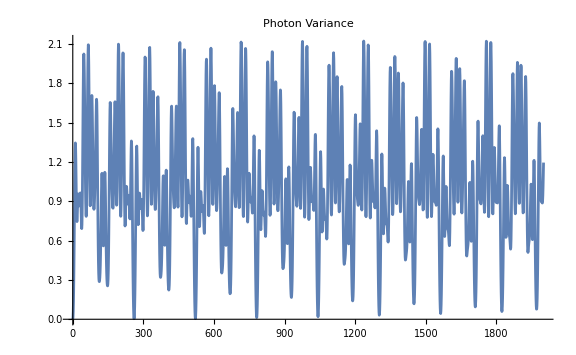

```mathematica
aDaggerA=KroneckerProduct[IdentityMatrix[2^K],a†.a];
aDaggerAsr = aDaggerA.aDaggerA;
photons=Table[Conjugate[ψs[[n]]].aDaggerA.ψs[[n]],{n,Length@tRange}];
ListLinePlot[{tRange,photons//Re}//Transpose,PlotRange->All,PlotLabel->"Total Photon Number", ImageSize->Large]

newPhotons=Table[Conjugate[ψs[[n]]].aDaggerAsr.ψs[[n]],{n,Length@tRange}] - photons^2;
ListLinePlot[{tRange,newPhotons//Re}//Transpose,PlotRange->All,PlotLabel->"Photon Variance", ImageSize->Large]
```